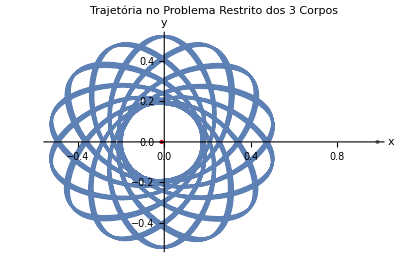

```mathematica
(*Definindo os parâmetros*)alpha=MoonMass/(EarthMass+MoonMass); (*Fração da massa da Lua*)
EarthMass=5.97219*10^24; (*kg*)
MoonMass=7.34767309*10^22; (*kg*)
alpha=MoonMass/(EarthMass+MoonMass); (*Valor de alpha*)

(*Distâncias adimensionais:Terra em (-alpha,0),Lua em (1-alpha,0)*)
d1[x_,y_]:=Sqrt[(x+alpha)^2+y^2]; (*Distância à Terra*)
d2[x_,y_]:=Sqrt[(x-(1-alpha))^2+y^2]; (*Distância à Lua*)

(*Potencial U(x,y)*)
U[x_,y_]:=-((1-alpha)/d1[x,y])-(alpha/d2[x,y])-(1/2)*(x^2+y^2);

(*Equações diferenciais do movimento*)
eq1=x''[t]==-D[U[x[t],y[t]],x[t]]+2*y'[t];
eq2=y''[t]==-D[U[x[t],y[t]],y[t]]-2*x'[t];

(*Condições iniciais-ajuste conforme necessário*)
x0=0.5; (*Posição inicial em x*)
y0=0.1; (*Posição inicial em y*)
vx0=0.0; (*Velocidade inicial em x*)
vy0=0.5; (*Velocidade inicial em y*)

(*Resolvendo as equações numericamente*)
sol=NDSolve[{eq1,eq2,x[0]==x0,y[0]==y0,x'[0]==vx0,y'[0]==vy0},{x,y},{t,0,100},Method->"StiffnessSwitching",MaxSteps->100000];

(*Plotando a trajetória*)
trajectory=ParametricPlot[Evaluate[{x[t],y[t]}/. sol],{t,0,100},PlotRange->All,AxesLabel->{"x","y"},PlotLabel->"Trajetória no Problema Restrito dos 3 Corpos"];

(*Mostrando o gráfico*)
Show[trajectory,Graphics[{Red,PointSize[Large],Point[{-alpha,0}]}],(*Terra*)Graphics[{Gray,PointSize[Medium],Point[{1-alpha,0}]}],(*Lua*)PlotRange->All]
```

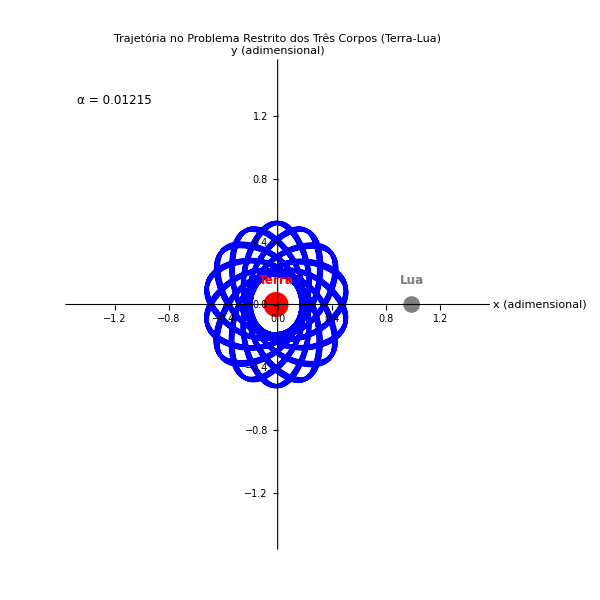

```mathematica
(*Parâmetros do Sistema*)EarthMass=5.97219*10^24;   (*Massa da Terra (kg)*)
MoonMass=7.34767309*10^22;  (*Massa da Lua (kg)*)
alpha=MoonMass/(EarthMass+MoonMass); (*Fração de massa da Lua*)

(*Distâncias adimensionais*)
d1[x_,y_]:=Sqrt[(x+alpha)^2+y^2]; (*Distância à Terra*)
d2[x_,y_]:=Sqrt[(x-(1-alpha))^2+y^2]; (*Distância à Lua*)

(*Potencial U(x,y)*)
U[x_,y_]:=-((1-alpha)/d1[x,y])-(alpha/d2[x,y])-(1/2)*(x^2+y^2);

(*Equações do Movimento*)
eq1=x''[t]==-D[U[x[t],y[t]],x[t]]+2*y'[t];
eq2=y''[t]==-D[U[x[t],y[t]],y[t]]-2*x'[t];

(*Condições Iniciais*)
x0=0.5;   (*Posição inicial em x*)
y0=0.1;   (*Posição inicial em y*)
vx0=0.0;  (*Velocidade inicial em x*)
vy0=0.5;  (*Velocidade inicial em y*)

(*Solução Numérica*)
sol=NDSolve[{eq1,eq2,x[0]==x0,y[0]==y0,x'[0]==vx0,y'[0]==vy0},{x,y},{t,0,100},Method->"StiffnessSwitching",MaxSteps->100000];

(*Plot da Trajetória*)
trajectoryPlot=ParametricPlot[Evaluate[{x[t],y[t]}/. sol],{t,0,100},PlotStyle->{Blue,Thickness[0.005]},PlotRange->{{-1.5,1.5},{-1.5,1.5}},AxesLabel->{"x (adimensional)","y (adimensional)"},LabelStyle->{FontFamily->"Times New Roman",FontSize->14},PlotLabel->Style["Trajetória no Problema Restrito dos Três Corpos (Terra-Lua)",14,Bold],ImageSize->600,Epilog->{{Red,PointSize[0.03],Point[{-alpha,0}],Text[Style["Terra",12,Bold],{-alpha,0.15}]},{Gray,PointSize[0.02],Point[{1-alpha,0}],Text[Style["Lua",12,Bold],{1-alpha,0.15}]},Text[Style[StringForm["α = ``",NumberForm[alpha,{4,5}]],12],{-1.2,1.3},Background->White]}];

(*Exibir o gráfico*)
Print[trajectoryPlot];
```

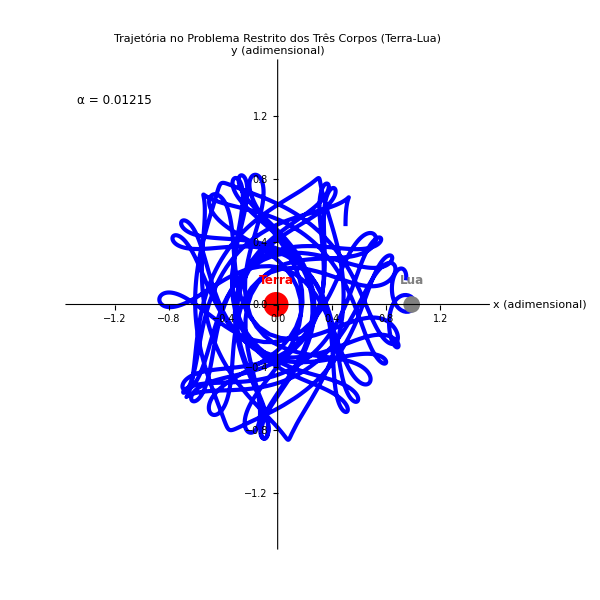

```mathematica
(*Parâmetros do Sistema*)EarthMass=5.97219*10^24;   (*Massa da Terra (kg)*)
MoonMass=7.34767309*10^22;  (*Massa da Lua (kg)*)
alpha=MoonMass/(EarthMass+MoonMass); (*Fração de massa da Lua*)

(*Distâncias adimensionais*)
d1[x_,y_]:=Sqrt[(x+alpha)^2+y^2]; (*Distância à Terra*)
d2[x_,y_]:=Sqrt[(x-(1-alpha))^2+y^2]; (*Distância à Lua*)

(*Potencial U(x,y)*)
U[x_,y_]:=-((1-alpha)/d1[x,y])-(alpha/d2[x,y])-(1/2)*(x^2+y^2);

(*Equações do Movimento*)
eq1=x''[t]==-D[U[x[t],y[t]],x[t]]+2*y'[t];
eq2=y''[t]==-D[U[x[t],y[t]],y[t]]-2*x'[t];

(*Condições Iniciais*)
x0=0.5;   (*Posição inicial em x*)
y0=0.5;   (*Posição inicial em y*)
vx0=0.0;  (*Velocidade inicial em x*)
vy0=0.5;  (*Velocidade inicial em y*)

(*Solução Numérica*)
sol=NDSolve[{eq1,eq2,x[0]==x0,y[0]==y0,x'[0]==vx0,y'[0]==vy0},{x,y},{t,0,100},Method->"StiffnessSwitching",MaxSteps->100000];

(*Plot da Trajetória*)
trajectoryPlot=ParametricPlot[Evaluate[{x[t],y[t]}/. sol],{t,0,100},PlotStyle->{Blue,Thickness[0.005]},PlotRange->{{-1.5,1.5},{-1.5,1.5}},AxesLabel->{"x (adimensional)","y (adimensional)"},LabelStyle->{FontFamily->"Times New Roman",FontSize->14},PlotLabel->Style["Trajetória no Problema Restrito dos Três Corpos (Terra-Lua)",14,Bold],ImageSize->600,Epilog->{{Red,PointSize[0.03],Point[{-alpha,0}],Text[Style["Terra",12,Bold],{-alpha,0.15}]},{Gray,PointSize[0.02],Point[{1-alpha,0}],Text[Style["Lua",12,Bold],{1-alpha,0.15}]},Text[Style[StringForm["α = ``",NumberForm[alpha,{4,5}]],12],{-1.2,1.3},Background->White]}];

(*Exibir o gráfico*)
Print[trajectoryPlot];
```